## Notes

This program extracts Apple Health data (.csv format)  and graphs and analyzes heart rate data.

## Initial Importing and Formatting Data Code

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jofre/Documents/GitHub/Connie_Summer2018

```mathematica
heartRate= Import["HKQuantityTypeIdentifierHeartRate.csv","CSV"];
```

```mathematica
(* extracts last column of data (heart rate)*)
getImportantData[ entries_List ]:= Part[ entries , All, -1];

(* gets second to last column in the data (time) *)
getDateString[ entry_String ]:= Part [ StringSplit[ entry ,";"] , -2] ;

(* gets last column of data which is heart rate value as a Number *)
getHeartRate[ entry_String ]:= ToExpression [Part [ StringSplit[ entry ,";"] , -1]] ;

(* gets last column of data  *)
getValue[ entry_String ]:= ToExpression [Part [ StringSplit[ entry ,";"] , -1]] ;
```

```mathematica
(* Dropping the first line, extract all rows and columns of heartrate data: *)
```

```mathematica
getImportantData[Drop[heartRate,1]]
```

{software:3.1>;count/min;2017-02-06 20:00:03 -0400;2017-02-06 19:58:53 -0400;2017-02-06 19:58:53 -0400;61,257626,software:4.3.1>;count/min;2018-07-04 14:30:46 -0400;2018-07-04 14:25:36 -0400;2018-07-04 14:25:36 -0400;71}
 |  |  |  |

```mathematica
(* Put in one time entry as formatted by apple watch, output DateObject to use to plot Mathematica *)
 getDateObject[ timeEntry_String ] := Module[{extractTZ, convertedString},
     extractTZ = StringTake[timeEntry , {-5, -1}];
     convertedString = DateObject[StringDrop[ timeEntry , -5],
             TimeZone -> Interpreter["TimeZone"][
                                                 StringJoin[" GMT-", ToString@Interpreter["Number"][StringTake[extractTZ, {2, 3}]]]
                                                 ]
                                  ];
    convertedString
  ]
   
   
  (* Apply getDateObject on all time datapoints *)
  (* Generate time column to plot heart rate data with *)
  getAllDateObjects [  entries_List ] := Map [ 
                                                 getDateObject[ 
                                                                getDateString [ # ]
                                                              ] &
                                                   ,
                                                   getImportantData[ entries ]
                                               ];
                                                   
 (* Generate heart rate column to plot *)
  getAllHeartPoints [  entries_List ] := Map [  
                                                getHeartRate
                                                , 
                                                getImportantData[ entries ] 
                                              ] ;                   

  (* Generate value column to plot *)
  getAllPoints [  entries_List ] := Map [  
                                                getValue
                                                , 
                                                getImportantData[ entries ] 
                                              ] ;
```

```mathematica
getAllDateObjects [Drop[heartRate, 1]]
```

```mathematica
heartRatePoints = getAllHeartPoints [ Drop[heartRate,1]]
```

{61,60,58,61,55,53,52,51,49,49,49,49,49,49,51,51,52,53,54,54,54,59,61,51,51,51,50,51,52,52,53,53,49,51,54,52,257556,72,69,62,68,57,57,68,64,63,62,63,66,71,66,76,70,68,77,94,81,80,68,67,79,83,75,81,82,69,71,77,79,68,75,70,71}
 |  |  |  |

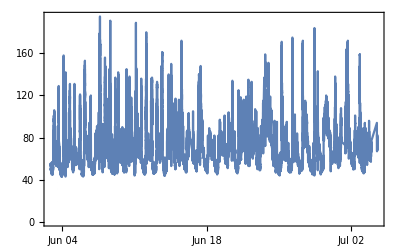

```mathematica
DateListPlot [ Take[Transpose[{dates, heartRatePoints}], -25000]]
```

```mathematica
SetDirectory[NotebookDirectory []]
```

/Users/jofre/Documents/GitHub/Connie_Summer2018

```mathematica
dates= Import[ "DateObject.mx"]
```

{Mon 6 Feb 2017 19:58:53GMT-4.,Mon 6 Feb 2017 20:03:21GMT-4.,Mon 6 Feb 2017 20:06:30GMT-4.,257622,Wed 4 Jul 2018 14:16:59GMT-4.,Wed 4 Jul 2018 14:22:11GMT-4.,Wed 4 Jul 2018 14:25:36GMT-4.}
 |  |  |  |

```mathematica
dateObjects= %131 ;
SetDirectory[NotebookDirectory []]
Export ["DateObject2.mx", dateObjects ,"MX" ]
```

DateObject::zone: Argument … in DateObject is not a recognized TimeZone specification.

/Users/jofre/Documents/GitHub/Connie_Summer2018

DateObject2.mx

## Import Saved Data

```mathematica
heartRatePoints = getAllHeartPoints [ Drop[heartRate,1]]
```

```mathematica
dobjs=Import["DateObject2.mx"];
```

```mathematica
DateListPlot [ Take[Transpose[{dobjs,heartRatePoints}],-25000]]
```

## Activity , resting HR

```mathematica
SetDirectory[NotebookDirectory []]
```

C:\Users\Connie\Downloads\Summer2018Starter-master\Summer2018Starter-master\Summer2018

```mathematica
(* Import sleep data *)
```

```mathematica
sleepData =Import["HKCategoryTypeIdentifierSleepAnalysis.csv","CSV"];
getImportantData[Drop[sleepData,1]]
```

getImportantData[{{HKCategoryTypeIdentifierSleepAnalysis;Clock;50;<<HKDevice: 0x1c469c980>,name:iPhone,manufacturer:Apple,model:iPhone,hardware:iPhone8,1,software:10.0.2>;2016-10-08 01:30:42 -0400;2016-10-07 20:17:24 -0400;2016-10-08 00:30:16 -0400;HKCategoryValueSleepAnalysisInBed},3296,{HKCategoryTypeIdentifierSleepAnalysis;AutoSleep;5.1.20;;2018-07-04 13:28:08 -0400;2018-07-04 09:45:00 -0400;2018-07-04 10:30:00 -0400;HKCategoryValueSleepAnalysisAsleep}}]
 |  |  |  |

```mathematica
sleepData//Length
```

3299

```mathematica
sleepData[[1]]
```

{type;sourceName;sourceVersion;device;creationDate;startDate;endDate;value}

```mathematica
sleepData[[14]]
```

{HKCategoryTypeIdentifierSleepAnalysis;Pillow;089;;2017-02-08 03:50:25 -0400;2017-02-07 20:33:31 -0400;2017-02-07 21:21:16 -0400;HKCategoryValueSleepAnalysisAsleep}

```mathematica
StringCases["HKCategoryValueSleepAnalysisAsleep",(_UpperCaseQ~~__LowerCaseQ)]
```

StringExpression::invld: Element _UpperCaseQ is not a valid string or pattern element in _UpperCaseQ~~__LowerCaseQ.

```mathematica
StringCases["HKCategoryValueSleepAnalysisAsleep",_?UpperCaseQ~~__?LowerCaseQ]
```

{Category,Value,Sleep,Analysis,Asleep}

```mathematica
{"HKCategoryValueSleepAnalysisDeepAsleep"}/."HKCategoryValueSleepAnalysisDeepAsleep"->"Deep Sleep"
```

{Deep Sleep}

```mathematica
(* Import resting heart rate data *)
restinghr = Import["HKQuantityTypeIdentifierRestingHeartRate.csv","CSV"];
```

```mathematica
getImportantData[Drop[restinghr,1]];
```

```mathematica
restinghr//Length
```

155

```mathematica
restinghr[[1]]
```

{type;sourceName;sourceVersion;unit;creationDate;startDate;endDate;value}

```mathematica
restinghrPoints = getAllPoints [Drop[ restinghr,1] ];
```

```mathematica
restinghrDates = getAllDateObjects [Drop[ restinghr,1] ];
```

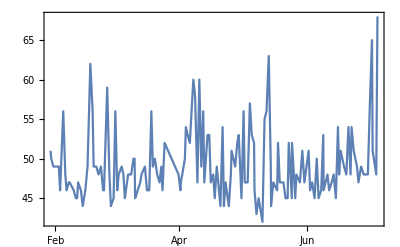

```mathematica
DateListPlot [ Take[Transpose[{restinghrDates,restinghrPoints}]]]
```

## Step Count

```mathematica
stepCount=Import["HKQuantityTypeIdentifierStepCount.csv","CSV"];
getImportantData[Drop[stepCount,1]]
```

{software:9.1>;count;2015-11-09 11:30:19 -0400;2015-11-09 10:28:53 -0400;2015-11-09 10:33:55 -0400;551,software:9.1>;count;2015-11-09 11:30:19 -0400;2015-11-09 10:33:55 -0400;2015-11-09 10:38:57 -0400;562,software:9.1>;count;2015-11-09 11:30:19 -0400;2015-11-09 10:38:57 -0400;2015-11-09 10:43:59 -0400;694,106093,software:4.3.1>;count;2018-07-04 13:51:34 -0400;2018-07-04 13:38:04 -0400;2018-07-04 13:43:56 -0400;18,software:4.3.1>;count;2018-07-04 14:06:34 -0400;2018-07-04 13:43:56 -0400;2018-07-04 13:48:57 -0400;12,software:4.3.1>;count;2018-07-04 14:21:34 -0400;2018-07-04 14:04:39 -0400;2018-07-04 14:14:39 -0400;26}
 |  |  |  |

```mathematica
stepCountDates = getAllDateObjects[Drop[stepCount,1]]
```

{Mon 9 Nov 2015 10:33:55GMT-4,Mon 9 Nov 2015 10:38:57GMT-4,Mon 9 Nov 2015 10:43:59GMT-4,Mon 9 Nov 2015 10:49:53GMT-4,Mon 9 Nov 2015 10:54:54GMT-4,Mon 9 Nov 2015 10:59:56GMT-4,Mon 9 Nov 2015 11:04:58GMT-4,Mon 9 Nov 2015 11:10:10GMT-4,Mon 9 Nov 2015 11:15:12GMT-4,Mon 9 Nov 2015 11:15:38GMT-4,Mon 9 Nov 2015 17:52:37GMT-4,106077,Wed 4 Jul 2018 13:01:53GMT-4,Wed 4 Jul 2018 13:04:02GMT-4,Wed 4 Jul 2018 13:15:13GMT-4,Wed 4 Jul 2018 13:33:24GMT-4,Wed 4 Jul 2018 13:43:22GMT-4,Wed 4 Jul 2018 13:43:58GMT-4,Wed 4 Jul 2018 13:23:55GMT-4,Wed 4 Jul 2018 13:33:08GMT-4,Wed 4 Jul 2018 13:43:56GMT-4,Wed 4 Jul 2018 13:48:57GMT-4,Wed 4 Jul 2018 14:14:39GMT-4}
 |  |  |  |

```mathematica
stepCountPoints=getAllPoints[Drop[stepCount,1]]
```

{551,562,694,580,224,815,546,431,506,26,359,333,14,400,290,300,311,372,269,16,499,558,639,488,83,208,488,690,791,325,549,21,34,251,323,9,308,369,360,165,10,15,18,16,440,543,647,624,65,168,417,17,398,126,31,18,16,22,357,374,336,427,367,30,393,418,155,21,20,459,521,506,573,122,334,504,825,526,752,205,762,539,484,490,82,192,466,19,433,558,122,104,431,193,409,216,403,480,470,490,468,452,456,477,467,206,66,87,105883,33,9,3,5,18,6,2,10,8,9,13,22,234,19,9,36,26,36,102,76,6,8,8,17,8,36,46,4,18,20,274,64,113,57,34,179,18,226,8,10,32,27,50,48,10,51,74,13,141,347,48,258,207,66,15,23,129,91,92,23,115,16,21,82,12,108,281,25,286,292,13,9,19,18,10,54,73,309,143,251,24,57,224,17,14,12,16,33,33,28,3,20,10,34,32,15,38,95,21,4,68,42,4,229,64,18,12,26}
 |  |  |  |

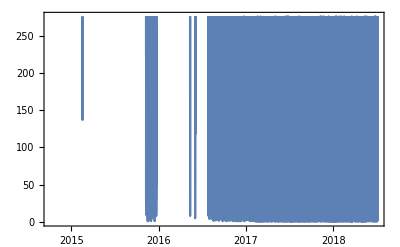

```mathematica
DateListPlot[Take[Transpose[{stepCountDates,stepCountPoints}]]]
```

```mathematica
DateHistogram[
```

acumulate points by day and stack them and use in date histogram

```mathematica
BarChart[stepCountPoints]
```

$Aborted

```mathematica
take averages and plot time series
```

create time series with date objects then ask for specific time range (wk by week)
total of steps per week